# 16 Stability of Householder QR

The plan is to look at Householder QR with our new tool.

f̃ is backwards stable if  f̃(x)=f(x̃) for some x̃ satisfying(|| x - x̃ ||)/(||x||)=O(ϵ_machine) 
“Backwards stable algorithm give the right answer to nearly the right question!”

## Understanding QR Behavior

### A→{Q,R}

As we have seen the built in Householder QR in all our tools produces exactly upper triangular Rs and almost orthogonal Qs that almost satisfy A=Q.R.  Mathematica is annoying because it gives us the Q on it side!

{6.98287×10^-16,1.68269×10^-15,4.0137}

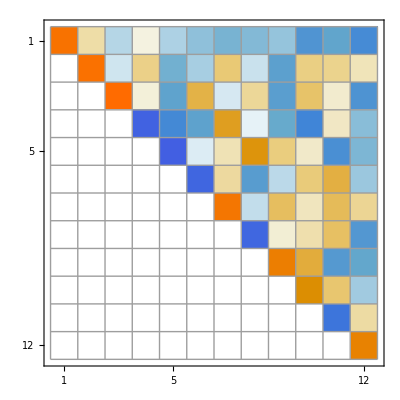

```mathematica
{m,n}={23,12};
A=RandomReal[{-1,1},{m,n}];
{Q,R}=QRDecomposition[A]; Q=Qᵀ;
Map[Norm,{Qᵀ.Q-IdentityMatrix[n],A-Q.R,A}]
MatrixPlot[R,Mesh->All]
```

### {Q_1,R_1}→Q_1.R_1=A→{Q_2,R_2}

The question now is how twitchy is the process.

```mathematica
{m,n}={52,25};
R1=UpperTriangularize[RandomReal[{-1,1},{n,n}]];
Q1=QRDecomposition[RandomReal[{-1,1},{m,n}]]⟦1⟧ᵀ;
A=Q1.R1; {Q2,R2}=QRDecomposition[A];Q2=Q2ᵀ;
TabView[{"R1"->MatrixPlot[R1,Mesh->All],"R2"->MatrixPlot[R2,Mesh->All]}];
TableForm[
Map[Norm,{A,A-Q1.R1,A-Q2.R2,Q1ᵀ.Q1-IdentityMatrix[n],Q2ᵀ.Q2-IdentityMatrix[n],R1-R2,Q1-Q2}],
TableHeadings->{{"||A||","res_1","res_2","orth_1","orth_2","||R1-R2||","||Q1-Q2||"}}]
```

||A|| | 4.07543
res_1 | 0.
res_2 | 3.99648×10^-15
orth_1 | 1.00863×10^-15
orth_2 | 1.29631×10^-15
||R1-R2|| | 1.93374×10^-12
||Q1-Q2|| | 2.26862×10^-11

What this means is that both the decompositions work but that they are not really all that similar! This means that the forward problem is ill-conditioned aka “twitchy”

## Unstable Example

### Bad News abut Char Polys

Whatever